### гр . 221703 Вечорко Д . Вариант 13

#### Задание 1 а1)

```mathematica
a=0;
b=1;
```

y'=y^2+ 0.7*x^2 + 5*y^2, y(0)=0;

```mathematica
h=0.1;
f[x_,y_] :=y^2+ 0.7*Sin[2x] ;
```

```mathematica
data = {{0,0}};
```

```mathematica
yb[n_]:=data[[n]][[2]]+h*f[data[[n]][[1]],data[[n]][[2]]]
```

{{0,0},{0.1,0.0139069},{0.2,0.0412145},{0.3,0.08106},{0.4,0.132338},{0.5,0.193816},{0.6,0.264225},{0.7,0.342358},{0.8,0.427137},{0.9,0.517708},{1.,0.613529}}

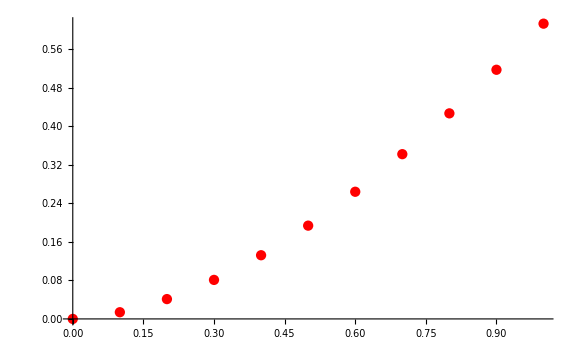

```mathematica
For[i=1,i<=b/h,i++,buff={a + i*h,data[[i]][[2]] + h/2*(f[a + i*h,data[[i]][[2]]] + f[a + i*h, yb[i]])};
AppendTo[data,buff];]
data
Pl1=ListPlot[data,PlotRange-> Full, ImageSize->Large, PlotStyle->Red]
```

#### а2)

```mathematica
h=0.05
```

0.05

{{0,0},{0.05,0.00349417},{0.1,0.0104491},{0.15,0.0208026},{0.2,0.0344674},{0.25,0.051335},{0.3,0.0712798},{0.35,0.0941628},{0.4,0.119835},{0.45,0.148141},{0.5,0.178921},{0.55,0.212016},{0.6,0.247267},{0.65,0.284522},{0.7,0.323633},{0.75,0.364465},{0.8,0.406892},{0.85,0.450805},{0.9,0.496113},{0.95,0.542744},{1.,0.590654}}

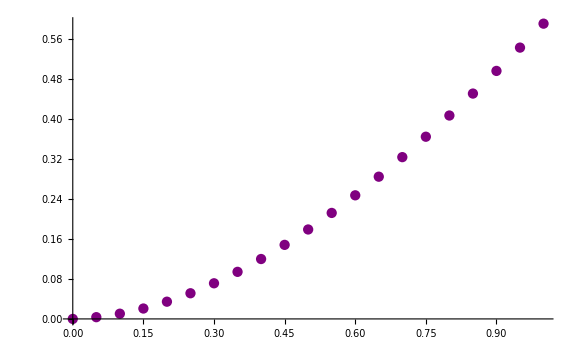

```mathematica
data = {{0,0}};
For[i=1,i<=b/h,i++,buff={a + i*h,data[[i]][[2]] + h/2*(f[a + i*h,data[[i]][[2]]] + f[a + i*h, yb[i]])};
AppendTo[data,buff];]
data
Pl2=ListPlot[data,PlotRange-> Full, ImageSize->Large, PlotStyle->Purple]
```

```mathematica
Clear[yb]
```

#### б1)

```mathematica
h=0.1;
data = {{0,0}};
x=a;y=data[[1]][[2]];
```

```mathematica
For[k=1,k<=b/h,k++,
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
x=x+h;y=y+(k1[x,y] + 2*k2[x,y] + 2*k3[x,y] + k4[x,y])/6;
buff={x,y};
AppendTo[data,buff];]
```

{{0,0},{0.1,0.0206643},{0.2,0.0543107},{0.3,0.0999286},{0.4,0.156317},{0.5,0.222188},{0.6,0.296257},{0.7,0.377327},{0.8,0.464364},{0.9,0.556582},{1.,0.653548}}

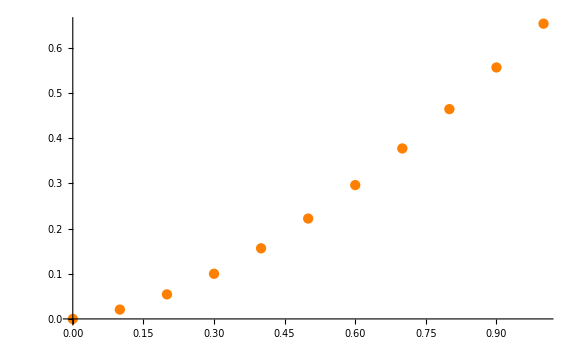

```mathematica
data
Pl3=ListPlot[data,PlotRange-> Full, ImageSize->Large, PlotStyle->Orange]
```

#### б2)

```mathematica
h=0.05;
data = {{0,0}};
x=a;y=data[[1]][[2]];
```

```mathematica
For[k=1,k<=b/h,k++,
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
x=x+h;y=y+(k1[x,y] + 2*k2[x,y] + 2*k3[x,y] + k4[x,y])/6;
buff={x,y};
AppendTo[data,buff];]
```

{{0,0},{0.05,0.00522855},{0.1,0.0138887},{0.15,0.025905},{0.2,0.0411788},{0.25,0.0595923},{0.3,0.0810123},{0.35,0.105294},{0.4,0.132284},{0.45,0.161823},{0.5,0.193752},{0.55,0.227909},{0.6,0.264137},{0.65,0.302285},{0.7,0.34221},{0.75,0.383779},{0.8,0.426871},{0.85,0.471386},{0.9,0.517237},{0.95,0.564364},{1.,0.612732}}

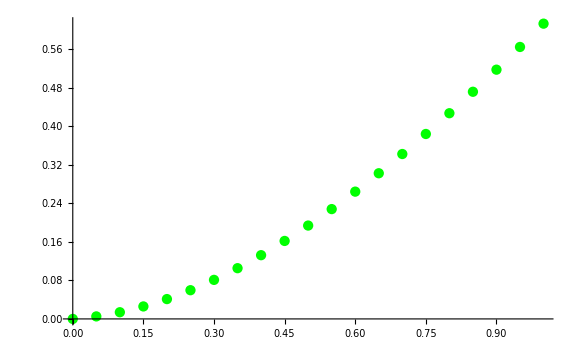

```mathematica
data4=data
ListPlot[data,ImageSize->Large,PlotRange->Full, PlotStyle->Green]
```

```mathematica
Clear[h,x,y,k1,k2,k3,k4,buff,data]
```

#### в)

```mathematica
data=DSolve[{y'[x]==f[x,y[x]],y[0]==0.8},y[x],x];
y1[x_]=y[x]/.Flatten[data]
```

-(1. (1. MathieuCPrime[0,-0.35,1/2 (-π/2+2. x)]-19.29 MathieuSPrime[0,-0.35,1/2 (-π/2+2. x)]))/(1. MathieuC[0,-0.35,1/2 (-π/2+2. x)]-19.29 MathieuS[0,-0.35,1/2 (-π/2+2. x)])

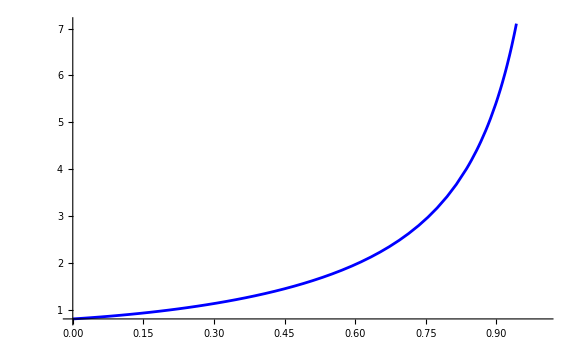

```mathematica
Pl5 = Plot[y1[x],{x,0,1},ImageSize->Large,PlotStyle->Blue]
```

```mathematica
data=NDSolve[{y'[x]==f[x,y[x]],y[0]==0},y[x],{x,a,b}]
```

{{y[x]→InterpolatingFunction[…][x]}}

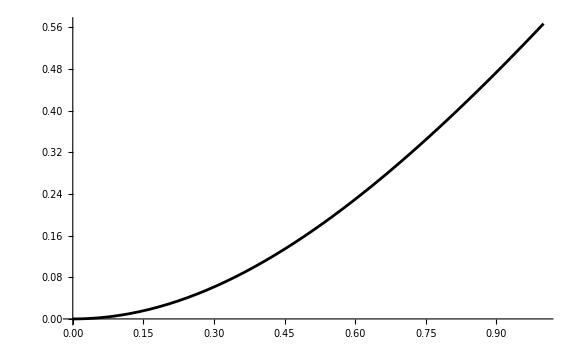

```mathematica
Pl6=Plot[Evaluate[y[x]/.data],{x,a,b},ImageSize->Large,PlotStyle->Black]
```

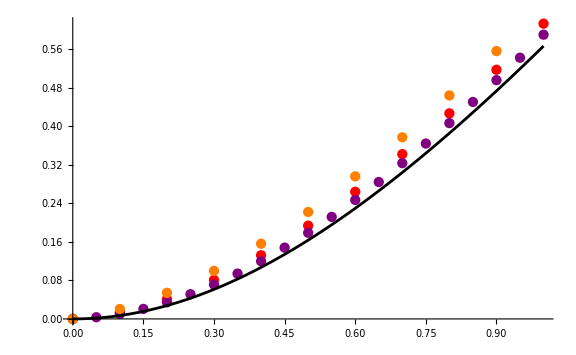

```mathematica
Show[Pl1,Pl2,Pl3,Pl5,Pl6,ImageSize->Large]
```

```mathematica
Clear[Pl1,Pl2,Pl3,Pl5,Pl6,data4,data,y1,f]
```

#### С ростом шага сетки точность метода Эйлера - Коши уменьшилась, а точность метода Рунге - Кутта 4 - го порядка увеличилась .

### Задание 2

Piecewise[{{y' + 5y + z = 2,, y[0]==1}, {z'+ 2y - z = cosx,, z[0]==1}}]

```mathematica
a=0;b=1;
fy[x_,y_,z_]:= 2 -5*y-z;
fz[x_,y_,z_]:=Cos[x]-2*y+z;
x0=0;y0=1;z0=1;
```

#### a1)

```mathematica
h=0.1;
```

```mathematica
datay={{x0,y0}};
dataz={{x0,z0}};
```

```mathematica
For[i=0;x1=x0;y1=y0;z1=z0,i<b/h,i++,
y1=y1+h*fy[x1,y1,z1];
z1=z1+h*fz[x1,y1,z1];
x1=x1+h;
AppendTo[datay,{x1,y1}];
AppendTo[dataz,{x1,z1}]];
datay
dataz
```

{{0,1},{0.1,0.6},{0.2,0.392},{0.3,0.27509},{0.4,0.200245},{0.5,0.143544},{0.6,0.0931962},{0.7,0.0432527},{0.8,-0.00944195},{0.9,-0.0667333},{1.,-0.129882}}

{{0,1},{0.1,1.08},{0.2,1.2091},{0.3,1.373},{0.4,1.56578},{0.5,1.78576},{0.6,2.03345},{0.7,2.31068},{0.8,2.62012},{0.9,2.96515},{1.,3.34981}}

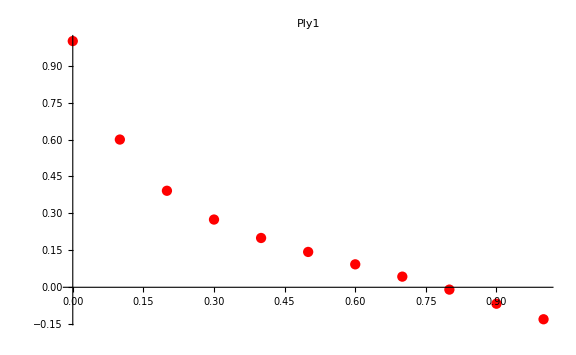

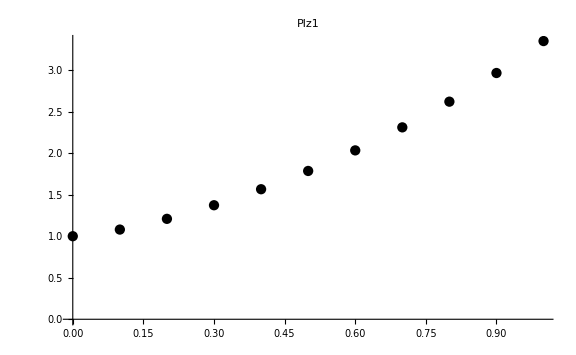

```mathematica
Ply1=ListPlot[datay,ImageSize->Large,PlotStyle->Red,PlotLabel->"Ply1"]
Plz1=ListPlot[dataz,ImageSize->Large,PlotStyle->Black,PlotLabel->"Plz1"]
```

#### a2)

```mathematica
h=0.05;
```

```mathematica
datay={{x0,y0}};
dataz={{x0,z0}};
```

```mathematica
For[i=0;x1=x0;y1=y0;z1=z0,i<b/h,i++,
y1=y1+h*fy[x1,y1,z1];
z1=z1+h*fz[x1,y1,z1];
x1=x1+h;
AppendTo[datay,{x1,y1}];
AppendTo[dataz,{x1,z1}]];
datay
dataz
```

{{0,1},{0.05,0.8},{0.1,0.649},{0.15,0.533948},{0.2,0.445201},{0.25,0.375632},{0.3,0.31997},{0.35,0.274313},{0.4,0.235771},{0.45,0.202196},{0.5,0.171992},{0.55,0.143965},{0.6,0.117219},{0.65,0.0910763},{0.7,0.0650197},{0.75,0.0386477},{0.8,0.011644},{0.85,-0.0162469},{0.9,-0.045237},{0.95,-0.0755084},{1.,-0.107223}}

{{0,1},{0.05,1.02},{0.1,1.05604},{0.15,1.10519},{0.2,1.16537},{0.25,1.23508},{0.3,1.31328},{0.35,1.39928},{0.4,1.49264},{0.45,1.59311},{0.5,1.70058},{0.55,1.8151},{0.6,1.93675},{0.65,2.06575},{0.7,2.20234},{0.75,2.34684},{0.8,2.4996},{0.85,2.66104},{0.9,2.83161},{0.95,3.01182},{1.,3.20222}}

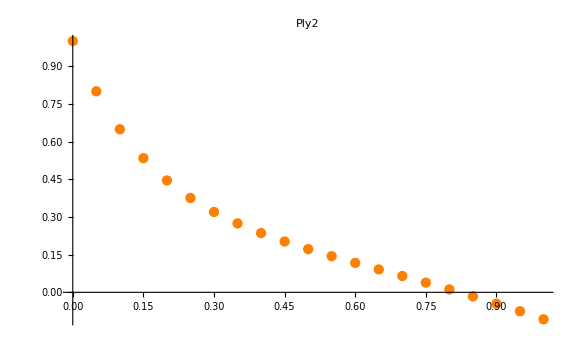

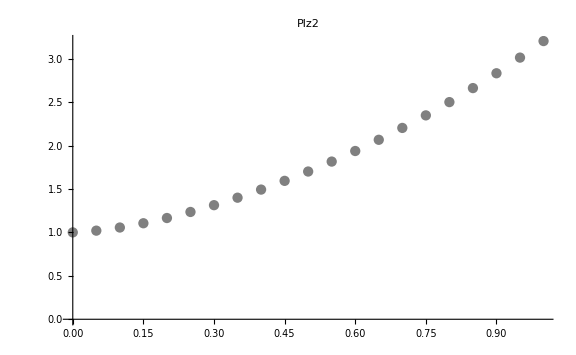

```mathematica
Ply2=ListPlot[datay,ImageSize->Large,PlotStyle->Orange,PlotLabel->"Ply2"]
Plz2=ListPlot[dataz,ImageSize->Large,PlotStyle->Gray,PlotLabel->"Plz2"]
```

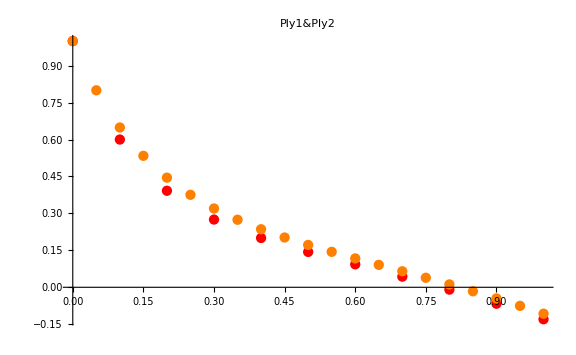

```mathematica
Show[Ply1,Ply2,PlotLabel->"Ply1&Ply2"]
```

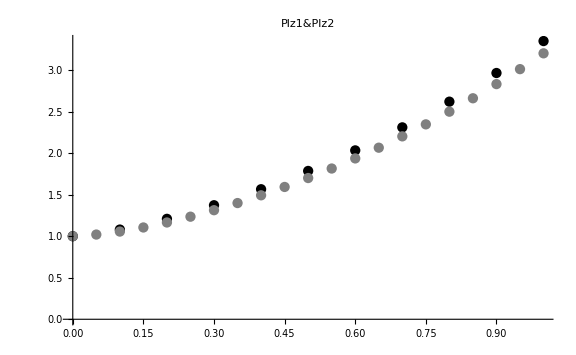

```mathematica
Show[Plz1,Plz2,PlotLabel->"Plz1&Plz2"]
```

```mathematica
Clear[datay,dataz,y1,z1,x1,i,h,Ply1,Ply2,Plz1,Plz2]
```

#### б1)

```mathematica
h=0.1;
datay={{x0,y0}};dataz={{x0,y0}};
```

```mathematica
For[rkx1=x0;rky1=y0;rkz1=z0;i=0, i<b/h,i++,
k1=h*fy[rkx1,rky1,rkz1];
r1=h*fz[rkx1,rky1,rkz1];
k2=h*fy[rkx1+h/2,rky1+k1/2,rkz1+r1/2];
r2=h*fz[rkx1+h/2,rky1+k1/2,rkz1+r1/2];
k3=h*fy[rkx1+h/2,rky1+k2/2,rkz1+r2/2];
r3=h*fz[rkx1+h/2,rky1+k2/2,rkz1+r2/2];
k4=h*fy[rkx1+h,rky1+k3,rkz1+r3];
r4=h*fz[rkx1+h,rky1+k3,rkz1+r3];
rkx1=rkx1+h; 
rky1=rky1+(k1+2*k2+2*k3+k4)/6;
rkz1=rkz1+(r1+2*r2+2*r3+r4)/6;
AppendTo[datay,{rkx1,rky1}];
AppendTo[dataz,{rkx1,rkz1}]];
datay
dataz
```

{{0,1},{0.1,0.684387},{0.2,0.487593},{0.3,0.359204},{0.4,0.269458},{0.5,0.200712},{0.6,0.142425},{0.7,0.08821},{0.8,0.0340842},{0.9,-0.0225538},{1.,-0.0835374}}

{{0,1},{0.1,1.03526},{0.2,1.12612},{0.3,1.25807},{0.4,1.42341},{0.5,1.61851},{0.6,1.84233},{0.7,2.09552},{0.8,2.37991},{0.9,2.69828},{1.,3.05424}}

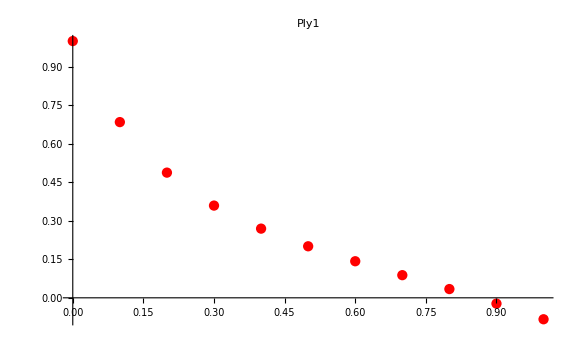

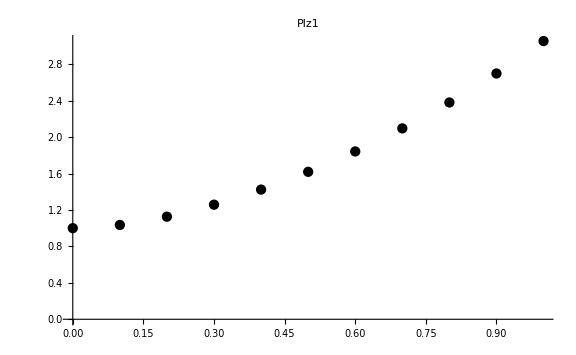

```mathematica
Ply1=ListPlot[datay,ImageSize->Large,PlotStyle->Red,PlotLabel->"Ply1"]
Plz1=ListPlot[dataz,ImageSize->Large,PlotStyle->Black,PlotLabel->"Plz1"]
```

#### б2)

```mathematica
h=0.05;
datay={{x0,y0}};dataz={{x0,y0}};
```

```mathematica
For[rkx1=x0;rky1=y0;rkz1=z0;i=0, i<b/h,i++,
k1=h*fy[rkx1,rky1,rkz1];
r1=h*fz[rkx1,rky1,rkz1];
k2=h*fy[rkx1+h/2,rky1+k1/2,rkz1+r1/2];
r2=h*fz[rkx1+h/2,rky1+k1/2,rkz1+r1/2];
k3=h*fy[rkx1+h/2,rky1+k2/2,rkz1+r2/2];
r3=h*fz[rkx1+h/2,rky1+k2/2,rkz1+r2/2];
k4=h*fy[rkx1+h,rky1+k3,rkz1+r3];
r4=h*fz[rkx1+h,rky1+k3,rkz1+r3];
rkx1=rkx1+h; 
rky1=rky1+(k1+2*k2+2*k3+k4)/6;
rkz1=rkz1+(r1+2*r2+2*r3+r4)/6;
AppendTo[datay,{rkx1,rky1}];
AppendTo[dataz,{rkx1,rkz1}]];
datay
dataz
```

{{0,1},{0.05,0.822899},{0.1,0.684166},{0.15,0.574651},{0.2,0.487333},{0.25,0.416822},{0.3,0.358976},{0.35,0.310612},{0.4,0.269279},{0.45,0.233089},{0.5,0.20058},{0.55,0.170622},{0.6,0.142333},{0.65,0.115022},{0.7,0.0881463},{0.75,0.0612698},{0.8,0.0340413},{0.85,0.00617159},{0.9,-0.0225824},{0.95,-0.0524301},{1.,-0.0835565}}

{{0,1},{0.05,1.00936},{0.1,1.03519},{0.15,1.07477},{0.2,1.12603},{0.25,1.18748},{0.3,1.258},{0.35,1.3368},{0.4,1.42335},{0.45,1.5173},{0.5,1.61847},{0.55,1.72679},{0.6,1.84231},{0.65,1.96515},{0.7,2.0955},{0.75,2.23365},{0.8,2.3799},{0.85,2.53463},{0.9,2.69828},{0.95,2.87131},{1.,3.05425}}

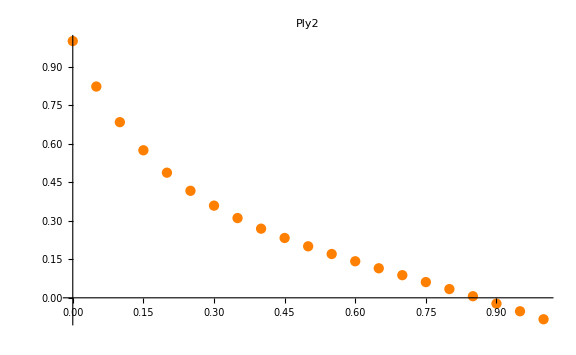

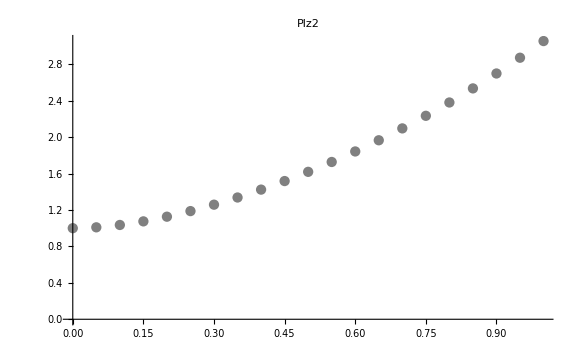

```mathematica
Ply2=ListPlot[datay,ImageSize->Large,PlotStyle->Orange,PlotLabel->"Ply2"]
Plz2=ListPlot[dataz,ImageSize->Large,PlotStyle->Gray,PlotLabel->"Plz2"]
```

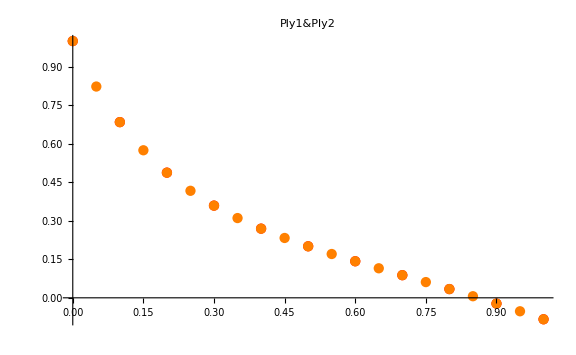

```mathematica
Show[Ply1,Ply2,PlotLabel->"Ply1&Ply2"]
```

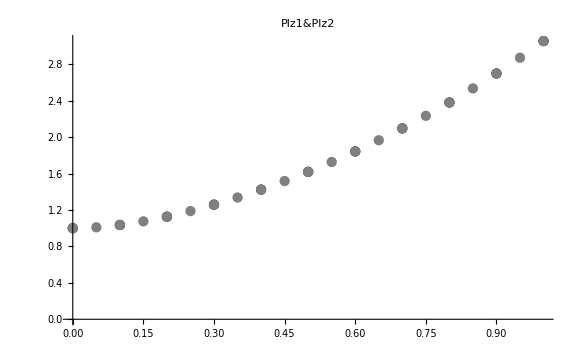

```mathematica
Show[Plz1,Plz2,PlotLabel->"Plz1&Plz2"]
```

```mathematica
Clear[Ply1,Ply2,Plz1,Plz2,datay,dataz,h,rkx1,rky1,rkz1,r1,r2,r3,r4,k1,k2,k3,k4,i]
```

#### в)

```mathematica
ds = DSolve[{y'[x]==fy[x,y[x],z[x]],y[x0]==y0,z'[x]==fz[x,y[x],z[x]],z[x0]==z0},{y[x],z[x]},x]
```

{{y[x]→-(ⅇ^(-2 x-√11 x-(-2+√11) x) (-880 ⅇ^(2 √11 x)-946 ⅇ^((-2+√11) x)-381 √11 ⅇ^((-2+√11) x)-946 ⅇ^(2 √11 x+(-2+√11) x)+381 √11 ⅇ^(2 √11 x+(-2+√11) x)-308 ⅇ^(2 √11 x) Cos[x]+154 ⅇ^(2 √11 x) Sin[x]))/3080,z[x]→(ⅇ^(-2 x-√11 x-(-2+√11) x) (1760 ⅇ^(2 √11 x)+1353 ⅇ^((-2+√11) x)-197 √11 ⅇ^((-2+√11) x)+1353 ⅇ^(2 √11 x+(-2+√11) x)+197 √11 ⅇ^(2 √11 x+(-2+√11) x)-1386 ⅇ^(2 √11 x) Cos[x]+1078 ⅇ^(2 √11 x) Sin[x]))/3080}}

```mathematica
dsy[x_] = y[x]/.Flatten[ds]
```

-(ⅇ^(-2 x-√11 x-(-2+√11) x) (-880 ⅇ^(2 √11 x)-946 ⅇ^((-2+√11) x)-381 √11 ⅇ^((-2+√11) x)-946 ⅇ^(2 √11 x+(-2+√11) x)+381 √11 ⅇ^(2 √11 x+(-2+√11) x)-308 ⅇ^(2 √11 x) Cos[x]+154 ⅇ^(2 √11 x) Sin[x]))/3080

```mathematica
dsz[x_] = z[x]/.Flatten[ds]
```

(ⅇ^(-2 x-√11 x-(-2+√11) x) (1760 ⅇ^(2 √11 x)+1353 ⅇ^((-2+√11) x)-197 √11 ⅇ^((-2+√11) x)+1353 ⅇ^(2 √11 x+(-2+√11) x)+197 √11 ⅇ^(2 √11 x+(-2+√11) x)-1386 ⅇ^(2 √11 x) Cos[x]+1078 ⅇ^(2 √11 x) Sin[x]))/3080

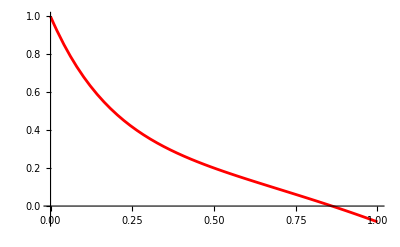

```mathematica
Pl1=Plot[dsy[x],{x,a,b},PlotStyle->Red]
```

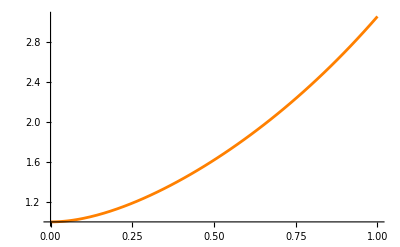

```mathematica
Pl2=Plot[dsz[x],{x,a,b},PlotStyle->Orange]
```

```mathematica
nds=NDSolve[{y'[x]==fy[x, y[x],z[x]],y[x0]==y0,z'[x]==fz[x, y[x],z[x]],z[x0]==z0},{y[x],z[x]},{x,a,b}]
```

{{y[x]→InterpolatingFunction[…][x],z[x]→InterpolatingFunction[…][x]}}

```mathematica
dsny[x_]=y[x]/.Flatten[nds];
dsnz[x_]=z[x]/.Flatten[nds];
```

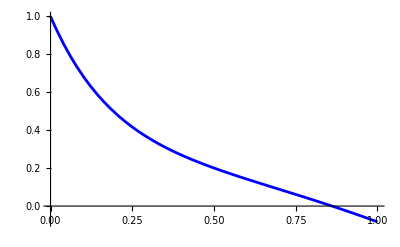

```mathematica
Pl3=Plot[dsny[x],{x,a,b},PlotStyle->Blue]
```

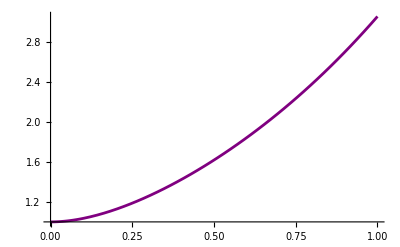

```mathematica
Pl4=Plot[dsnz[x],{x,a,b},PlotStyle->Purple]
```

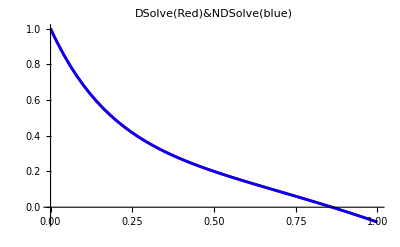

```mathematica
Show[Pl1,Pl3,PlotLabel->"DSolve(Red)&NDSolve(blue)"]
```

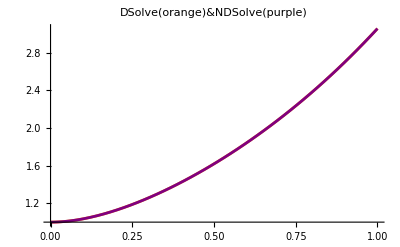

```mathematica
Show[Pl2,Pl4,PlotLabel->"DSolve(orange)&NDSolve(purple)"]
```

```mathematica
Clear[Pl1,Pl2,Pl3,Pl4,a,b,ds,nds,dsy,dsz,dsny,dsnz,fy,fz,x0,y0,z0]
```

#### Наибольшую точность показал метод Рунге - Кутта 4 - го порядка .